# Load Files

```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];

Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
Get[FileNameJoin[{Directory[],"DifferentialOperator.m"}]];
$P=2^31-1;
PureIntegrals=ReadList[FileNameJoin[{NotebookDirectory[],"BubblePureInts.txt"}]];
SetDirectory[NotebookDirectory[]];

(*LaportaBasis=ReadList[FileNameJoin[{Directory[],"masters"}]];
LaportaBasis=Cases[LaportaBasis,_ptb,Infinity];*)
```

# Generate Phase-Space Point

```mathematica
tPoint=GetRandomPT[0,$P]
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
(*samplepoint=1;
SubReduList=Get[ToString[StringForm["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone/KIRA/splitres/phasespace_00002.m",IntegerString[samplepoint,10,5]]]];
tPoint=Thread[Rule[invariants,SubReduList[[2,1]]]]

reductionRules=ReductionRules=GetReductionTableFromList[SubReduList[[2,2]]];*)


epsrepl={(ep->(4-d)/2)/.tPoint};
PureIntegralN=Expand[PureIntegrals/.tPoint/.epsrepl/.root[n_]:>PowerMod[n,1/2,$P],Modulus->$P]//EchoTiming;
diffOp=getDifferentialOperator[tPoint];
checkDifferentialOperator[tPoint,diffOp]
```

{d→1610692278,mt2→905274710,s12→81377422,s123→564335935,s16→248221797,s23→1133990189,s234→1029710898,s34→342078712,s345→991474079,s45→245801001,s56→1624613449}

0.000452

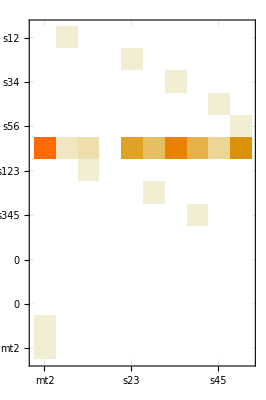

Δ6=0

∂_(RowBox[{) Δ6=0

∂_(RowBox[{) Δ6=0

∂_(RowBox[{) Δ6=0

«7 more identical outputs»

# Compute Basis Change Matrix

9

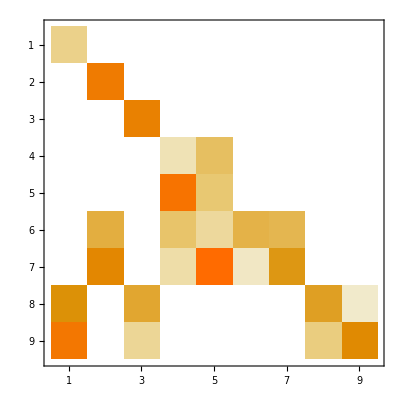

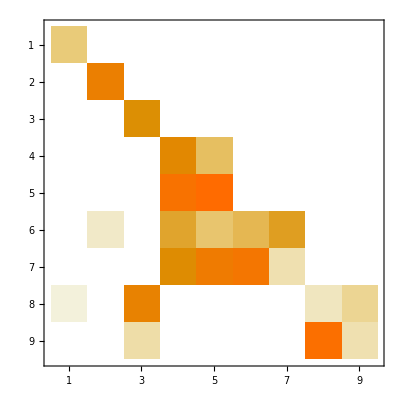

```mathematica
reductionRules=GetReductionTableFromFile[FileNameJoin[{NotebookDirectory[],"KIRA/results/hxb/numerics_2147483647_0.m"}]];
Ureduce=ReadList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];
ExtraRelations=GetExtraRelationReplacements[reductionRules,tPoint];
PureIntegralN2=Expand[PureIntegralN/.reductionRules,Modulus->$P];
PureIntegralN3=Expand[PureIntegralN2/.ExtraRelations,Modulus->$P];

NonZeros=Cases[reductionRules,_hxb,Infinity]//DeleteDuplicates;
ZeroInts=Complement[Ureduce,NonZeros];
ZeroIntsRepl=Thread[Rule[ZeroInts,0]];
PureIntegralN4=Expand[PureIntegralN3/.ExtraRelations/.ZeroIntsRepl,Modulus->$P];
Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates//Length
SubLaporta=Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates;

PureIntegralN4=Expand[PureIntegralN4/.epsrepl,Modulus->$P];

BasisChangMat=Table[CoefficientArrays[PureIntegralN4[[pos]],SubLaporta],{pos,1,Length[PureIntegralN]}];
BasisChangMat=Normal[BasisChangMat[[All,2]]];
BasisChangMatInv=Inverse[BasisChangMat,Modulus->$P];
BasisChangMat//MatrixPlot
BasisChangMatInv//MatrixPlot
```

# Compute DE Matrix Pre IBP

```mathematica
loopMomentumScalarProductsT=Expand[loopMomentumScalarProducts/.tPoint,Modulus->$P];
mandelstamScalarProductsT=Expand[mandelstamScalarProducts/.tPoint,Modulus->$P];
DeleteList=Delete[{1,2,3,4,5,6,7,8,9,10,11},Position[tPoint[[All,1]],s16]];
Monitor[diffInts=Table[
Expand[Expand[(applyDifferentialOperator[Collect[Coefficient[diffOp,ds[invariantsnodUpperCase[[var]]]],del[___]],Expand[PureIntegrals[[intpos]]/.tPoint[[DeleteCases[DeleteList,var+1]]]/.epsrepl,Modulus->$P]]/.tPoint/.root'[x_]:>1/(2 root[x]))/.root[x_]:>PowerMod[x,1/2,$P],Modulus->$P]/.loopMomentumScalarProductsT/.mandelstamScalarProductsT,Modulus->$P],{var,1,Length[invariantsnodUpperCase]},{intpos,1,Length[PureIntegrals]}],Row[{ProgressIndicator[(var-1)*241+intpos,{1,241*10}],"  ",var,"/10 ",intpos,"/241"}]];
```

## Extra Step If Redu List does not exit yet

```mathematica
ToReduce=Cases[diffInts,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}],ToReduce];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}]];

ToReduce2=Cases[PureIntegralN,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}],ToReduce2];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];

(*GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ExtraRelationsReduList.txt"}]];*)

DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
WriteJobFile[{"UReduList","ReduList"}]
```

104

9

# Apply IBP Reduction

```mathematica
diffIntsIBREDUCED=Expand[diffInts/.reductionRules/.ExtraRelations,Modulus->$P];
NonReduced=Cases[diffIntsIBREDUCED,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
NullInts2=Complement[NonReduced,SubLaporta];
diffIntsIBREDUCED=diffIntsIBREDUCED/.Thread[Rule[NullInts2,0]];
```

9

# Compute DE Matrices

```mathematica
dhxbMatrices=Table[Normal[CoefficientArrays[diffIntsIBREDUCED[[i,j]],SubLaporta]/.{0}->{0,ConstantArray[0,Length[PureIntegralN]]}][[2]],{i,1,Length[invariants]-1},{j,1,Length[SubLaporta]}];
Mplot1=MatrixPlot[Expand[dhxbMatrices[[1]].BasisChangMatInv,Modulus->$P]];
Mplot2=MatrixPlot[Expand[dhxbMatrices[[2]].BasisChangMatInv,Modulus->$P]];
Mplot3=MatrixPlot[Expand[dhxbMatrices[[3]].BasisChangMatInv,Modulus->$P]];
Mplot4=MatrixPlot[Expand[dhxbMatrices[[4]].BasisChangMatInv,Modulus->$P]];
Mplot5=MatrixPlot[Expand[dhxbMatrices[[5]].BasisChangMatInv,Modulus->$P]];
Mplot6=MatrixPlot[Expand[dhxbMatrices[[6]].BasisChangMatInv,Modulus->$P]];
Mplot7=MatrixPlot[Expand[dhxbMatrices[[7]].BasisChangMatInv,Modulus->$P]];
Mplot8=MatrixPlot[Expand[dhxbMatrices[[8]].BasisChangMatInv,Modulus->$P]];
Mplot9=MatrixPlot[Expand[dhxbMatrices[[9]].BasisChangMatInv,Modulus->$P]];
Mplot10=MatrixPlot[Expand[dhxbMatrices[[10]].BasisChangMatInv,Modulus->$P]];
GraphicsGrid[{{Mplot1,Mplot2,Mplot3,Mplot4,Mplot5},{Mplot6,Mplot7,Mplot8,Mplot9,Mplot10}}]
```

-Graphics-